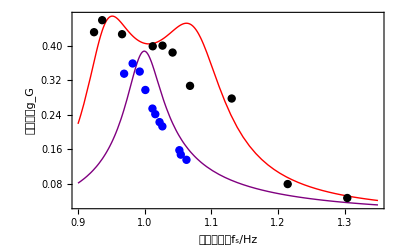

```mathematica
Clear[w,Rl,g,Lp,Ls,Cp,Cs,ghudao,k,x];
Lp=Ls=52×10^-6;
Cp=Cs=220×10^-9;
Uin=1;
fr=47050;

k=0.157;
M=√(Lp×Ls)×k;
Rp=0.05;
Rs=0.05;
w=x*fr;
s=2*π*w*I;
R1=Rp+(s*Lp+1/(s*Cp));
R2=Rs+Rl+(s*Ls+1/(s*Cs));
Rf=(s*M)^2/R2;
ghudao= (s×M)/(R1×R2-(s×M)^2);
ghudao=Sqrt[ComplexExpand[Re[FullSimplify[ghudao]]]^2+ComplexExpand[Im[FullSimplify[ghudao]]]^2];
a=0.8;
b=0.7;
p1=Plot[Evaluate@Table[ghudao,{Rl,2.4,2.4,1}],{x,0.9,1.35},
PlotRange->{0,0.6},
Frame->True,
FrameLabel->{Style["(:5f52:4e00:5316:9891:7387f)_s/Hz",Black],Style["(:8de8:5bfc:589e:76cag)_G",Black]},
PlotLegends->Placed[{"R_L=2.4Ω(仿真)"},{a,b}],
(*PlotLabel->Style["(:4e0d:540c:8d1f:8f7d:7535:963bR)_L下，(:4e92:5bfc:589e:76caG)_h(:4e0e:9891:7387f)_s的关系",Black,Bold],*)
PlotStyle->{{Red,Thick},{Blue,Thick},{Purple,Thick},{Pink,Thick},{Orange,Thick}}];

p2=Plot[Evaluate@Table[ghudao,{Rl,8,8,1}],{x,0.9,1.35},
PlotRange->{0,0.6},
Frame->True,
FrameLabel->{Style["(:5f52:4e00:5316:9891:7387f)_s/Hz",Black],Style["(:4e92:5bfc:589e:76cag)_G",Black]},
PlotLegends->Placed[{"R_L=8Ω(仿真)"},{a,b}],
(*PlotLabel->Style["(:4e0d:540c:8d1f:8f7d:7535:963bR)_L下，(:4e92:5bfc:589e:76caG)_h(:4e0e:9891:7387f)_s的关系",Black,Bold],*)
PlotStyle->{{Purple,Thick},{Red,Thick},{Blue,Thick},{Purple,Thick},{Pink,Thick},{Orange,Thick}}];




dist4=Import["D:/data/WPT2.4I.csv"];
p4=ListPlot[dist4,InterpolationOrder->2,Mesh->Full,
PlotLegends->Placed[{"   R_L=2.4Ω(实测)"},{a,b}],
Frame->True,
DataRange->{0,10},

PlotStyle->{Black,Thick}];
dist3=Import["D:/data/wpts8I.csv"];
p3=ListPlot[dist3,InterpolationOrder->2,Mesh->Full,
PlotLegends->Placed[{"   R_L=8Ω(实测)"},{a,b}],
PlotStyle->{Blue,Thick}];

Show[p1,p2,p3,p4,PlotRange->All]
```